## PHAS0012: Computing for Mathematical Physics

# Exercises 2: Lists

```mathematica
Clear["Global`*"]
```

Click on the line above and press Shift+Enter to start the exercise with a clean slate. 
 Use Mathematica's built-in help as much as you like.

The exercises use the following lists: execute the following cell to generate the list, but do not edit it in any way.

```mathematica
mat={{a,b,c},{d,e,f},{g,h,i}};
vec={I,π,E};
coins={1,2,5,10,20,50,100};
names={{"Fred","Smith"},{"Ali","Khan"},{"Marie","Lefrant"},{"Joe","Bloggs"},{"Humphrey","Earwicker"}};
pd=ToExpression[Delete[Characters[ToString[N[Pi,1000]]],2]];
```

1. Using the matrix mat and the vector vec given above:
     a) extract the second row of mat
     b) extract the second column of mat, using Transpose
     d) take the matrix product of mat with vec
     e) take the scalar product of vec mat vec
      f) confirm that vec.transpose(mat) = mat.vec.

```mathematica
q1a = mat[[2]]
```

{d,e,f}

```mathematica
q1bmat = Transpose[mat]
```

{{a,d,g},{b,e,h},{c,f,i}}

```mathematica
q1bmat[[2]]
```

{b,e,h}

```mathematica
q1cproduct = mat vec
```

{{ⅈ a,ⅈ b,ⅈ c},{d π,e π,f π},{ⅇ g,ⅇ h,ⅇ i}}

```mathematica
q1dscalar =
```

```mathematica
q1e1 = vec.transpose(mat)
```

{{a {ⅈ,π,ⅇ}.transpose,b {ⅈ,π,ⅇ}.transpose,c {ⅈ,π,ⅇ}.transpose},{d {ⅈ,π,ⅇ}.transpose,e {ⅈ,π,ⅇ}.transpose,f {ⅈ,π,ⅇ}.transpose},{g {ⅈ,π,ⅇ}.transpose,h {ⅈ,π,ⅇ}.transpose,i {ⅈ,π,ⅇ}.transpose}}

```mathematica
q1e2 = mat.vec
```

{ⅈ a+c ⅇ+b π,ⅈ d+ⅇ f+e π,ⅈ g+ⅇ i+h π}

```mathematica
q1e1 == q1e2
```

{{a {ⅈ,π,ⅇ}.transpose,b {ⅈ,π,ⅇ}.transpose,c {ⅈ,π,ⅇ}.transpose},{d {ⅈ,π,ⅇ}.transpose,e {ⅈ,π,ⅇ}.transpose,f {ⅈ,π,ⅇ}.transpose},{g {ⅈ,π,ⅇ}.transpose,h {ⅈ,π,ⅇ}.transpose,i {ⅈ,π,ⅇ}.transpose}}=={ⅈ a+c ⅇ+b π,ⅈ d+ⅇ f+e π,ⅈ g+ⅇ i+h π}

2. The list coins gives the values in pence of the coins in circulation in the UK up to a value of £1. How many different values from zero up to and including £2 can be made up using three coins or fewer (the coins need not all be different but at least one coin must be used)?

Form the list of values up to and including £2 that cannot be made up in this way. How many are there? 

What is the smallest and what is the largest in the range that cannot be made?

Check that the sum of the number that can be made and the number that cannot is 201.  Expect to use Outer, Flatten, Union, Intersection, Complement, Count, and Table or Range.

```mathematica
7 8 8
```

```mathematica
i = 1
j = 1
k = 1
```

1

1

1

```mathematica
q2table = Table[Take[coins, {i}] +  Take[coins, {j}] + Take[coins, {k}], {i,7},{j,7},{k,7}];
```

```mathematica
q2values ={{3},{4},{7},{12},{22},{52},{102},{4},{5},{8},{13},{23},{53},{103},{7},{8},{11},{16},{26},{56},{106},{12},{13},{16},{21},{31},{61},{111},{22},{23},{26},{31},{41},{71},{121},{52},{53},{56},{61},{71},{101},{151},{102},{103},{106},{111},{121},{151},{201},{4},{5},{8},{13},{23},{53},{103},{5},{6},{9},{14},{24},{54},{104},{8},{9},{12},{17},{27},{57},{107},{13},{14},{17},{22},{32},{62},{112},{23},{24},{27},{32},{42},{72},{122},{53},{54},{57},{62},{72},{102},{152},{103},{104},{107},{112},{122},{152},{202},{7},{8},{11},{16},{26},{56},{106},{8},{9},{12},{17},{27},{57},{107},{11},{12},{15},{20},{30},{60},{110},{16},{17},{20},{25},{35},{65},{115},{26},{27},{30},{35},{45},{75},{125},{56},{57},{60},{65},{75},{105},{155},{106},{107},{110},{115},{125},{155},{205},{12},{13},{16},{21},{31},{61},{111},{13},{14},{17},{22},{32},{62},{112},{16},{17},{20},{25},{35},{65},{115},{21},{22},{25},{30},{40},{70},{120},{31},{32},{35},{40},{50},{80},{130},{61},{62},{65},{70},{80},{110},{160},{111},{112},{115},{120},{130},{160},{210},{22},{23},{26},{31},{41},{71},{121},{23},{24},{27},{32},{42},{72},{122},{26},{27},{30},{35},{45},{75},{125},{31},{32},{35},{40},{50},{80},{130},{41},{42},{45},{50},{60},{90},{140},{71},{72},{75},{80},{90},{120},{170},{121},{122},{125},{130},{140},{170},{220},{52},{53},{56},{61},{71},{101},{151},{53},{54},{57},{62},{72},{102},{152},{56},{57},{60},{65},{75},{105},{155},{61},{62},{65},{70},{80},{110},{160},{71},{72},{75},{80},{90},{120},{170},{101},{102},{105},{110},{120},{150},{200},{151},{152},{155},{160},{170},{200},{250},{102},{103},{106},{111},{121},{151},{201},{103},{104},{107},{112},{122},{152},{202},{106},{107},{110},{115},{125},{155},{205},{111},{112},{115},{120},{130},{160},{210},{121},{122},{125},{130},{140},{170},{220},{151},{152},{155},{160},{170},{200},{250},{201},{202},{205},{210},{220},{250},{300}};
```

```mathematica
Union[q2values]
```

{{3},{4},{5},{6},{7},{8},{9},{11},{12},{13},{14},{15},{16},{17},{20},{21},{22},{23},{24},{25},{26},{27},{30},{31},{32},{35},{40},{41},{42},{45},{50},{52},{53},{54},{56},{57},{60},{61},{62},{65},{70},{71},{72},{75},{80},{90},{101},{102},{103},{104},{105},{106},{107},{110},{111},{112},{115},{120},{121},{122},{125},{130},{140},{150},{151},{152},{155},{160},{170},{200},{201},{202},{205},{210},{220},{250},{300}}

3. Sort the list names into alphabetical order of second names. Do this by using the RotateLeft and RotateRight functions as well as Sort.

```mathematica
names
```

{{Fred,Smith},{Ali,Khan},{Marie,Lefrant},{Joe,Bloggs},{Humphrey,Earwicker}}

```mathematica
q3names = Transpose[names]
```

{{Fred,Ali,Marie,Joe,Humphrey},{Smith,Khan,Lefrant,Bloggs,Earwicker}}

```mathematica
q3names = RotateRight[q3names]
```

{{Smith,Khan,Lefrant,Bloggs,Earwicker},{Fred,Ali,Marie,Joe,Humphrey}}

```mathematica
q3names =Transpose[q3names]
```

{{Smith,Fred},{Khan,Ali},{Lefrant,Marie},{Bloggs,Joe},{Earwicker,Humphrey}}

```mathematica
q3names =Sort[q3names]
```

{{Bloggs,Joe},{Earwicker,Humphrey},{Khan,Ali},{Lefrant,Marie},{Smith,Fred}}

```mathematica
q3names = Transpose[q3names]
```

{{Bloggs,Earwicker,Khan,Lefrant,Smith},{Joe,Humphrey,Ali,Marie,Fred}}

```mathematica
q3names = RotateRight[q3names]
```

{{Joe,Humphrey,Ali,Marie,Fred},{Bloggs,Earwicker,Khan,Lefrant,Smith}}

```mathematica
q3names = Transpose[q3names]
```

{{Joe,Bloggs},{Humphrey,Earwicker},{Ali,Khan},{Marie,Lefrant},{Fred,Smith}}

4. The list pd contains the first thousand digits in the decimal representation of π. Generate a table giving the frequencies of the digits 0 to 9 in that list. Check that the total of the frequencies is 1000.

```mathematica
q4freq = Table[Count[pd, i], {i,9}]
```

{116,103,103,93,97,94,95,100,106}

```mathematica
q4freq  =Insert[q4freq, Count[pd, 0], 1]
```

{93,116,103,103,93,97,94,95,100,106}

```mathematica
Total[q4freq]
```

1000

5. Generate a table of 1000 random integers in the range 1 to 1000 (use the Help file on Random if necessary). Count how many are prime numbers. How many distinct prime numbers are there in the list? Generate a list of the form {{first prime number, number of occurrences in original list},{second prime,..}..}.

```mathematica
q5table = Table[Random[Integer, {0, 1000}], {i, 1000}];
```

```mathematica
q5primelist = {2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541,547,557,563,569,571,577,587,593,599,601,607,613,617,619,631,641,643,647,653,659,661,673,677,683,691,701,709,719,727,733,739,743,751,757,761,769,773,787,797,809,811,821,823,827,829,839,853,857,859,863,877,881,883,887,907,911,919,929,937,941,947,953,967,971,977,983,991,997};
```

```mathematica
q5primesinlist =Intersection[q5table, q5primelist]
```

{2,3,5,7,17,29,31,37,41,43,47,61,71,83,89,97,103,109,113,127,131,137,149,163,173,179,181,191,193,197,199,211,223,227,229,241,257,263,269,271,277,281,283,317,331,337,349,353,359,379,383,389,397,401,409,419,421,431,433,449,457,463,487,491,499,509,521,523,541,547,563,571,577,587,607,613,617,619,643,653,691,701,719,727,743,773,787,797,821,823,827,839,853,857,877,883,907,919,937,947,953,967,971,983,997}

```mathematica
Length[q5primesinlist]
```

105

```mathematica
Table[{q5primesinlist [[i]], Count[q5table, q5primesinlist [[i]]]}, {i, Length[q5primesinlist]}]
```

{{2,1},{3,3},{5,1},{7,2},{17,1},{29,1},{31,2},{37,2},{41,1},{43,4},{47,1},{61,1},{71,1},{83,1},{89,2},{97,1},{103,1},{109,1},{113,1},{127,1},{131,1},{137,1},{149,2},{163,2},{173,1},{179,2},{181,2},{191,2},{193,3},{197,2},{199,1},{211,1},{223,2},{227,2},{229,1},{241,3},{257,1},{263,1},{269,1},{271,2},{277,1},{281,1},{283,1},{317,1},{331,2},{337,3},{349,1},{353,1},{359,1},{379,1},{383,2},{389,1},{397,1},{401,1},{409,1},{419,2},{421,1},{431,2},{433,1},{449,1},{457,1},{463,1},{487,2},{491,1},{499,1},{509,1},{521,1},{523,1},{541,2},{547,1},{563,2},{571,1},{577,3},{587,1},{607,1},{613,2},{617,1},{619,2},{643,2},{653,1},{691,3},{701,3},{719,1},{727,1},{743,1},{773,1},{787,1},{797,3},{821,2},{823,1},{827,1},{839,3},{853,1},{857,1},{877,3},{883,1},{907,2},{919,1},{937,1},{947,3},{953,3},{967,3},{971,2},{983,1},{997,1}}

6. The time taken by Mathematica can increase quite rapidly for complex tasks. Explore this, using the fact that Timing[task;] will return an expression of the form {3.1 Second,Null}. 
Generate a list (table) of the times taken to simplify the expansion of (a+b+c+d + e + f+8)^n for n running from 1 to 12, and plot the result.
Note: Mathematica is clever about remembering results it has obtained before, so if you generate the table of times a second time it will be much quicker. Get around this by choosing a different integer instead of 8 in the expansion for subsequent runs, or better yet, use the ClearSystemCache function which you can just place at the start of your cell.

```mathematica
n = 1
```

1

```mathematica
q6timing =Table[Timing[Simplify[Expand[(a + b + c + d + e + f + 8)^n];]], {n,12}]
```

{{0.,Null},{0.,Null},{0.,Null},{0.,Null},{0.,Null},{0.,Null},{0.,Null},{0.,Null},{0.015625,Null},{0.015625,Null},{0.015625,Null},{0.03125,Null}}

```mathematica
q6justtime = List[Transpose[q6timing][[1]]]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.015625,0.015625,0.015625,0.03125}}

```mathematica
q6nvalues = {1,2,3,4,5,6,7,8,9,10,11,12}
```

{1,2,3,4,5,6,7,8,9,10,11,12}

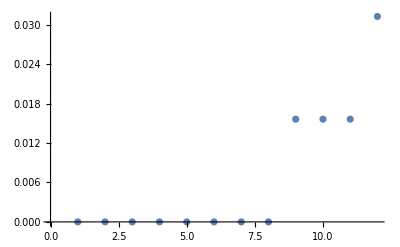

Plot::pllim: Range specification {{0.,0.,0.,0.,0.,0.,0.,0.015625,0.,0.015625,0.03125,0.03125}} is not of the form {x, xmin, xmax}.

Plot[x,q6justtime]

```mathematica
ListPlot[q6justtime]
```

A.H. Harker, J Underwood, J Bhamrah
UCL
January 2008, revised January 2009, January 2015, January 2017, January 2018, January 2019